```mathematica
ClearAll[p, Ng, P]
Ng  = 4;
p=1/2;
P[a_/; a == Ng, b_]:= 1;
P[a_, b_/; b == Ng] := 0;
P[a_, b_]:=P[a, b]=p P[a + 1, b] + (1 - p) P[a, b + 1];

P[1,0]
```

21/32

```mathematica
Table[Sum[Binomial[2 (Ng - 1), i],{i, 0, Ng-1}]/4^(Ng-1), {Ng, 1, 10}]
```

```mathematica
{1,3/4,11/16,21/32,163/256,319/512,1255/2048,2477/4096,39203/65536,77691/131072}
```

```mathematica
1255*2
```

2510

```mathematica
Simplify[P[1,0, Ng] - P[0,1, Ng], Assumptions->{p>0, p< 1, Ng > 0}]
```

```mathematica
Numerator[231/□
```

```mathematica
319* 2
```

```mathematica
42 * 4
```

168

```mathematica
Plot[P[1,0, Ng] - P[0,1, Ng], {Ng, 2, 3}]
```

TerminatedEvaluation[RecursionLimit]

```mathematica
FactorInteger[231]
```

{{3,1},{7,1},{11,1}}

```mathematica
Denominator[12155/65536]
```

65536

```mathematica
FactorInteger[65536]
```

{{2,16}}

231/1024

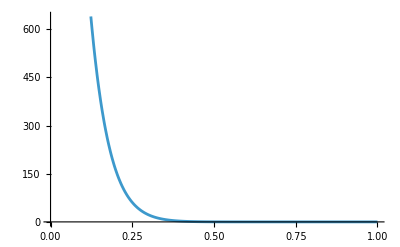

```mathematica
Plot[-(-1+p)^9 (4862-31824 p+92820 p^2-157080 p^3+168300 p^4-116688 p^5+51051 p^6-12870 p^7+1430 p^8),{p,0,1}]
```

```mathematica
Simplify[%74]
```

-(-1+p)^6 (-132+495 p-770 p^2+616 p^3-252 p^4+42 p^5)

```mathematica
Simplify[1/2 (1/2 (1-p)^2+(1-p) (1+(1-p)/2-p))-(1/2 (1-p)^2+(1-p) (1+(1-p)/2-p)) (1-p)-1/2 (1-p)^3+(1-p) (1+1/2 (1+(1-p)/2-p)-p)]
```

1/4 (-1+p)^2 (1+10 p)

```mathematica
Simplify[(1-p) ((1-p) (1-p+(1-p+(1-p) (1-q)) (1-q))+((1-p) (1-p+(1-p) (1-q))+(1-p)^2 (1-q)) (1-q))+((1-p) ((1-p) (1-p+(1-p) (1-q))+(1-p)^2 (1-q))+(1-p)^3 (1-q)) (1-q)]
```

1/2

```mathematica
ClearAll[P,p];
p=1/2;

(*boundary conditions*)
P[a_Integer,b_Integer,n_Integer]/;a==n:=1;
P[a_Integer,b_Integer,n_Integer]/;b==n:=0;

(*recursive step with memoization*)
P[a_Integer,b_Integer,n_Integer]/;a<=n&&b<=n:=P[a,b,n]=(1-p) P[a+1,b,n]+p P[a,b+1,n];
```

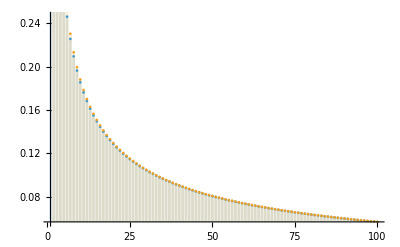

1/2

```mathematica
DiscretePlot[{P[1,0,n] - P[0, 1, n], 1/(Sqrt[Pi (n - 1)])}, {n, 1, 100}]
P[0,0,3]
```